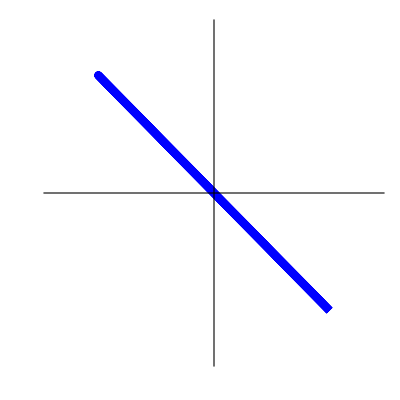

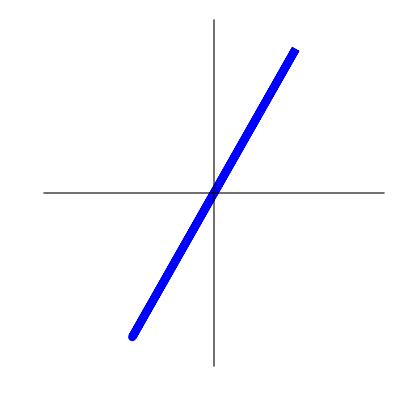

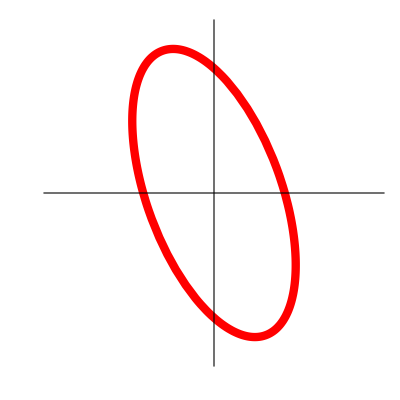

```mathematica
rad=1;
diagPol= ParametricPlot[{rad Cos[π/4] Cos[t], rad Sin[-π/4] Cos[t]}, {t, 0,2 π}, Axes->True, PlotStyle->{Blue, Arrowheads[{0.2,0.2}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
interMedLinearPol= ParametricPlot[{rad Cos[π/3] Cos[t], rad Sin[π/3] Cos[t]}, {t, 0,2 π}, Axes->True, PlotStyle->{Blue, Arrowheads[{0.2,0.2}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
ellipticalPol =  ParametricPlot[{rad Cos[π/3] Cos[t], rad Sin[π/3] Cos[t-(2π)/3]}, {t, 0,2 π}, Axes->True, PlotStyle->{Red, Arrowheads[{ 0, 0, 0.2, 0, 0, 0.2, 0}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
SetDirectory[NotebookDirectory[]];
Export["diag_pol.svg", diagPol];
Export["intermediate_linear.svg", interMedLinearPol];
Export["elliptical_pol.svg", ellipticalPol];
```

```mathematica
χ = π/3;
ϕ = (2π)/3;
outJones = {Cos[χ], Sin[χ] ⅇ^(ⅈ ϕ)};
```

-Graphics3D-

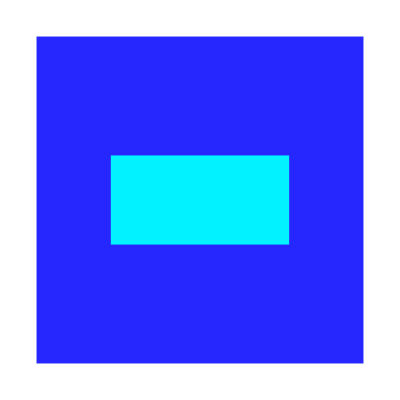

```mathematica
width = 3;
length = 1.5;
height = 4.75;
basez = 7;
basexy=5.5;
post = Graphics3D[{Cyan,Opacity[0.95], Cuboid[{-width/2, -length/2, 0},{width/2, length/2, height}], Opacity[0.85],Blue, Cuboid[{-basexy/2, -basexy/2, -basez},{basexy/2, basexy/2, 0}]}, Boxed->False, BoxStyle->Directive[Gray, Dashed], Lighting->{{"Directional",White,{{1.5,-1.5,0.75},{0,1,0}}}}, ViewPoint->{0.75, -1.5, 1}]
toppost = Graphics[{Opacity[0.85],Blue, Rectangle[{-basexy/2, -basexy/2},{basexy/2, basexy/2}], Cyan,Opacity[0.95],Rectangle[{-width/2, -length/2},{width/2, length/2}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["post.eps", post]
Export["post_topview.eps", toppost]
```

post.eps

post_topview.eps

0.1

0.35

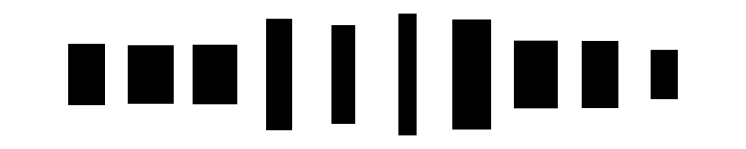

```mathematica
sep = 0.42;
mindim = 0.1
maxdim = 0.35
n=10;
rects = Table[
xdim = RandomReal[{mindim, maxdim}];
ydim = RandomReal[{mindim, maxdim}];
Rectangle[{-xdim/2+sep i, -ydim/2},{xdim/2 + sep i, ydim/2}], {i, 1, n}];
rectGraphic =Graphics[{Black, rects}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["rect_graphic.svg", rectGraphic]
```

rect_graphic.svg

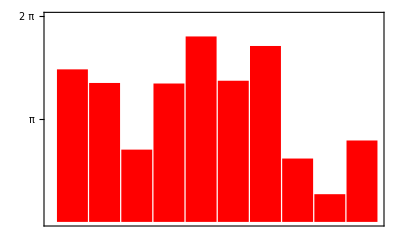

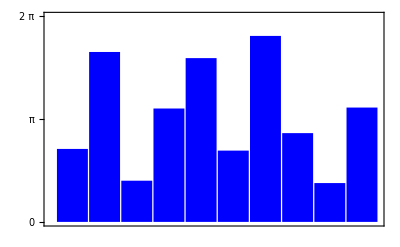

```mathematica
phiY = Table[RandomReal[{0, 2π}],{i, 1, n}];
phiX =Table[RandomReal[{0, 2π}],{i, 1, n}];
xchart=BarChart[phiX,ChartBaseStyle->{Red,EdgeForm[None]}, Frame->{True, True,True, True}, FrameTicks->{{{{π,π, {0.02,0}}, {2π,2π, {0.02,0}}}, None}, {None, None}}, PlotRange->{Automatic, {0, 2π}} , FrameStyle->Directive[Thickness[0.002]], BarSpacing->0.04, FrameTicksStyle->Directive[{FontSize->0, FontFamily->"Times"}]]
ychart=BarChart[phiY,ChartBaseStyle->{Blue,EdgeForm[None]}, Frame->{True, True,True, True}, FrameTicks->{{{0, {π,π, {0.02,0}}, {2π,2π, {0.02,0}}}, None}, {None, None}}, PlotRange->{Automatic, {0, 2π}} , FrameStyle->Directive[Thickness[0.002]], BarSpacing->0.04, FrameTicksStyle->Directive[{FontSize->0, FontFamily->"Times"}]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["phi_x.eps", xchart];
Export["phi_y.eps", ychart];
```

```mathematica
SetDirectory[NotebookDirectory[]];
x="x";
y="y";
z="z";
pi = "π";
tau = "2π";
zero = "0";
bigphix = "(Φ⃗)_x";
integral = Style["1/(2  π)(∫^d)_0e^(ⅈ SubscriptBox[ϕ, x])e^(ⅈ FractionBox[2  π m, d])dx", FontFamily->"Perpetua", FontSize->50];
set = Style["{c_x^m, c_x^y}", FontFamily->"Perpetua", FontSize->50]; 
epsilon = Style["ϵ", FontFamily->"Perpetua", FontSize->50]; 

Export["x.eps", x]
Export["y.eps", y]
Export["z.eps", z]
Export["pi.eps", pi]
Export["tau.eps", tau]
Export["big_phi_x.eps", bigphix]
Export["integral.eps", integral]
Export["epsilon.eps", epsilon]
```

x.eps

y.eps

z.eps

pi.eps

tau.eps

big_phi_x.eps

integral.eps

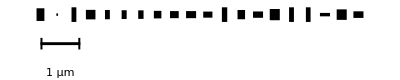

C:\Users\Noah\Dropbox\Github repo II\Graphics\poincare_sphere_graphics

C:\Users\Noah\Dropbox\Github repo II\Graphics

CreateDirectory::filex: C:\Users\Noah\Dropbox\Github repo II\Graphics\N20_Stokes_420nm already exists.

$Failed

C:\Users\Noah\Dropbox\Github repo II\Graphics\N20_Stokes_420nm

N20_stokes_schematic.eps

C:\Users\Noah\Dropbox\Github repo II\Graphics\poincare_sphere_graphics

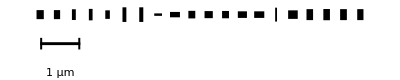

C:\Users\Noah\Dropbox\Github repo II\Graphics

CreateDirectory::filex: C:\Users\Noah\Dropbox\Github repo II\Graphics\N20_Stokes_420nm already exists.

$Failed

C:\Users\Noah\Dropbox\Github repo II\Graphics\N20_Stokes_420nm

N20_O4_schematic.eps

```mathematica
xDiamsStokes = {0.1974, 0.0420, 0.1218, 0.2394, 0.1218,0.1260, 0.1344, 0.1890, 0.2184, 0.2520, 0.2310, 0.1344, 0.1890, 0.2520, 0.2520, 0.1218, 0.1176,0.2520,0.2520,0.2520};
yDiamsStokes = {0.2184, 0.0420, 0.2520, 0.1638, 0.1596, 0.1512, 0.1470,0.1302, 0.1218, 0.1218, 0.1050, 0.2520, 0.1596, 0.1092,0.1932, 0.2520, 0.2520, 0.0588, 0.1806,0.1134};
xDiams4 = {0.1806, 0.1554, 0.0966, 0.0924, 0.1134, 0.0966, 0.1008, 0.1932, 0.2478, 0.1722, 0.2058, 0.1722, 0.2268, 0.2520, 0.0462, 0.2394, 0.1638, 0.1638, 0.1680, 0.1554};
yDiams4 = {0.1554, 0.1554, 0.1848, 0.1974, 0.1470, 0.2520, 0.2520, 0.0420, 0.0924, 0.1302, 0.1218, 0.1260, 0.1134, 0.1134, 0.2394, 0.1470, 0.1890, 0.1932, 0.1890, 0.1890};
sep = 0.42;
scalebar = 1;
scaleheight=0.05;
scaleoffset = 0.5;
barheight=0.2;

rectsStokes =Table[
Rectangle[{(-xDiamsStokes_⟦i⟧)/2+sep i, (-yDiamsStokes_⟦i⟧)/2},{xDiamsStokes_⟦i⟧/2 + sep i, yDiamsStokes_⟦i⟧/2}], {i, 1, Length[xDiamsStokes]}];
scaleStokes = {Rectangle[{sep, -scaleheight/2-scaleoffset}, {scalebar+sep, scaleheight/2-scaleoffset}], Rectangle[{sep, -barheight/2-scaleoffset},{sep+scaleheight, barheight/2-scaleoffset}], Rectangle[{sep+scalebar-scaleheight, -barheight/2-scaleoffset},{sep+scalebar, barheight/2-scaleoffset}], Style[Text[ToString[scalebar]<>" μm", {sep+scalebar/2, -2*scaleoffset}], FontFamily->"Perpetua", FontSize->20]};
rectGraphicStokes =Graphics[{Black, rectsStokes, scaleStokes}]
SetDirectory[NotebookDirectory[]]
SetDirectory[".."]
CreateDirectory["N20_Stokes_420nm"]
SetDirectory["N20_Stokes_420nm"]
Export["N20_stokes_schematic.eps", rectGraphicStokes]
SetDirectory[NotebookDirectory[]]
rects4 =Table[
Rectangle[{(-xDiams4_⟦i⟧)/2+sep i, (-yDiams4_⟦i⟧)/2},{xDiams4_⟦i⟧/2 + sep i, yDiams4_⟦i⟧/2}], {i, 1, Length[xDiams4]}];
scale4= {Rectangle[{sep, -scaleheight/2-scaleoffset}, {scalebar+sep, scaleheight/2-scaleoffset}], Rectangle[{sep, -barheight/2-scaleoffset},{sep+scaleheight, barheight/2-scaleoffset}], Rectangle[{sep+scalebar-scaleheight, -barheight/2-scaleoffset},{sep+scalebar, barheight/2-scaleoffset}], Style[Text[ToString[scalebar]<>" μm", {sep+scalebar/2, -2*scaleoffset}], FontFamily->"Perpetua", FontSize->20]};
rectGraphic4=Graphics[{Black, rects4, scale4}]

SetDirectory[".."]
CreateDirectory["N20_Stokes_420nm"]
SetDirectory["N20_Stokes_420nm"]
Export["N20_O4_schematic.eps", rectGraphic4]
```